```mathematica
wykres[l_,z_]:=Module[{indexin,indexout,retab,imtab,val},

indexin =Position[inltab,l];

retab=Table[{funkcjatabin[[indexin[[1,1]],i,1]],funkcjatabin[[indexin[[1,1]],i,2]]},{i,1,Length[funkcjatabin[[indexin[[1,1]]]]]}];
imtab=Table[{funkcjatabin[[indexin[[1,1]],i,1]],funkcjatabin[[indexin[[1,1]],i,3]]},{i,1,Length[funkcjatabin[[indexin[[1,1]]]]]}];

val=Show[ListPlot[{imtab,retab},PlotRange->{{0,40},{-z,z}}],Plot[{funkcjataboutre[[l+1]],funkcjataboutim[[l+1]]},{r,0,60},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->z]];

Return[val];
];
```

```mathematica
kk =0.686;
path  = "/home/mateusz/workspace/photo_fit/";
```

```mathematica
inpaths=FileNames[StringJoin["z1_k",ToString[SetAccuracy[kk,4]],"*"],StringJoin[path,"input/"]];
outpaths=FileNames[StringJoin["fit_z1_k",ToString[SetAccuracy[kk,4]],"*"],StringJoin[path,"output/"]];
```

```mathematica
infiles=Table[FileNameTake[inpaths[[i]]],{i,1,Length[inpaths]}];
outfiles=Table[FileNameTake[outpaths[[i]]],{i,1,Length[outpaths]}];
```

```mathematica
inltab=Table[ToExpression[StringCases[infiles[[i]],DigitCharacter..][[4]]],{i,1,Length[infiles]}];
```

```mathematica
funkcjatabin=Table[Import[inpaths[[i]]],{i,1,Length[inpaths]}];
 funkcjatabout=Table[Import[outpaths[[i]]],{i,1,Length[outpaths]}];
```

```mathematica
maxL = (Length[funkcjatabout[[1]]]-1)/ 11 -1;
```

```mathematica
funkcjataboutre=Table[Sum[funkcjatabout[[1, 2 + j*11 + i,3]]*r^j*Exp[-funkcjatabout[[1, 2 + j*11 + i,2]]*r^2] * funkcjatabout[[1, 2 + j*11 + i,2]]^(0.75 + j/2.),{i,1,10}],{j,0,maxL}];

funkcjataboutim=Table[Sum[funkcjatabout[[1, 2 + j*11 + i,4]]*r^j*Exp[-funkcjatabout[[1, 2 + j*11 + i,2]]*r^2]* funkcjatabout[[1, 2 + j*11 + i,2]]^(0.75 + j/2.),{i,1,10}],{j,0,maxL}];
```

```mathematica
ll=3;
```

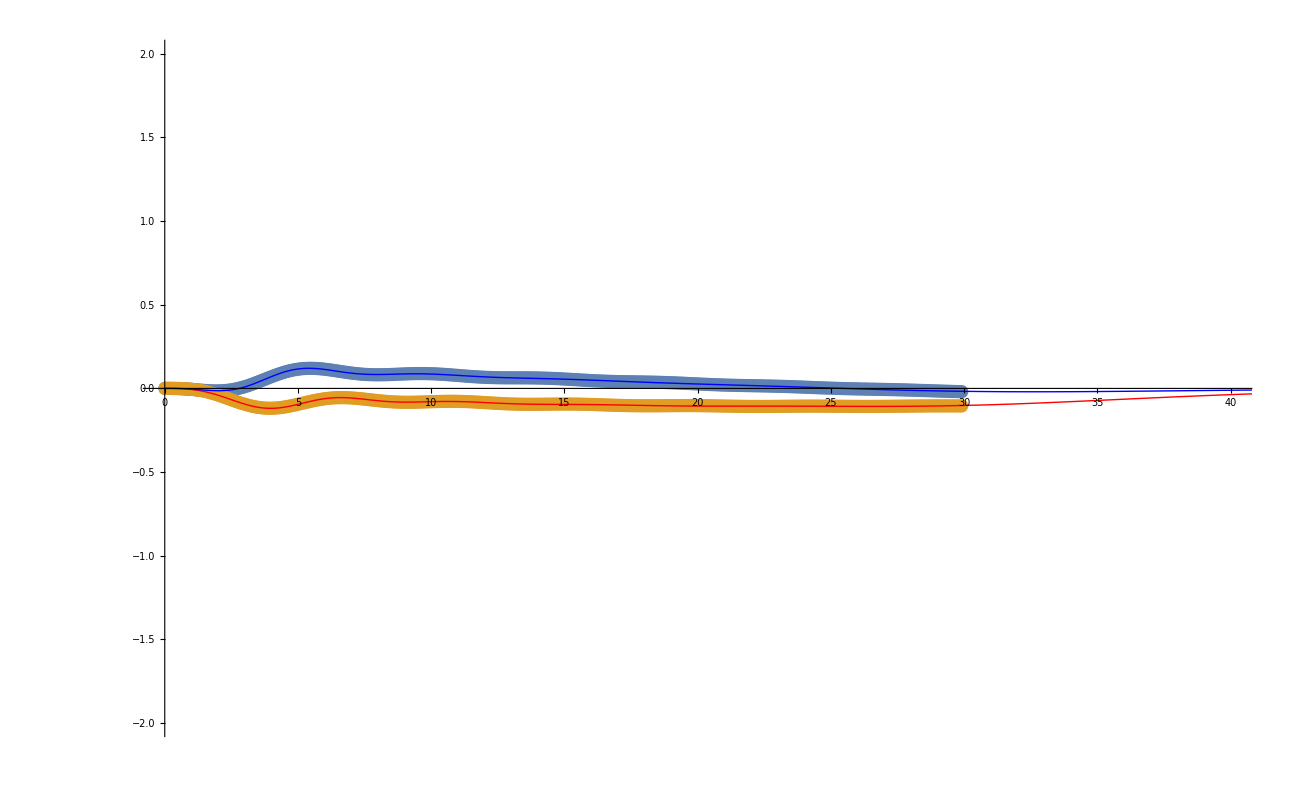

```mathematica
wykres[ll,2]
```

```mathematica
ToOldFormat=Table[{Table[funkcjatabout[[1, 2 + j*11 + i,2]],{i,1,10}],
Table[funkcjatabout[[1, 2 + j*11 + i,3]]* funkcjatabout[[1, 2 + j*11 + i,2]]^(0.75 + j/2.) ,{i,1,10}], 
Table[funkcjatabout[[1, 2 + j*11 + i,4]]* funkcjatabout[[1, 2 + j*11 + i,2]]^(0.75 + j/2.) ,{i,1,10}]}, {j,0,maxL}];
For[l = 0, l≤maxL, l++,
Export[StringJoin["/home/mateusz/Documents/continuum_fits/output/fit_z1_k", ToString[SetAccuracy[kk,4]], "_l",ToString[l],".dat"],ToOldFormat[[l+1]]];]
```